```mathematica
Functions
```

Functions

```mathematica
PDeath[day_,accept_,endp_]:=Module[{a,b,p},
a=accept[[;;,day,2]]/Total[accept[[;;,day,2]]];
(*Probability that outbreak has died out*)
b=endp[[;;,day,2]];
p=Total[a*b];
Return[p];
];

(*Note: Mean sizes may be inaccurate if sizes are calculated with a cap*)
FindMeanSize[s_,val_]:=Module[{ss,m},
ss=s[[val]];
m=Total[Table[ss[[i,1]]*ss[[i,2]],{i,1,Length[ss]}]];
Return[m];
];

FindMedianSize[s_,val_]:=Module[{ss,cs,med},
ss=s[[val]];
cs=ss;
For[i=2,i<=Length[ss],i++,
cs[[i,2]]=cs[[i,2]]+cs[[i-1,2]];
];
med=Select[cs,#[[2]]>=0.5&][[1,1]];
Return[med];
];

fourParamChartStyle={RGBColor["#4477AA"],RGBColor["#117733"],RGBColor["#DDCC77"],RGBColor["#CC6677"]};
```

```mathematica
Import Data
```

Data Import

```mathematica
SetDirectory["/Users/johnfozard/OINK/output_variable_infection_length"];
p=0.04;
times=Flatten[Import["/Users/johnfozard/OINK/Data/Time_points.dat","Table"]];
accept4=Table[Import[ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist4=Table[Import[ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist4=Table[Import[ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist4],i++,
origdist4[[i,;;,1]]=-origdist4[[i,;;,1]];
];
pend4=Import[ToString[p]<>"/P_Outbreak_End.dat","Table"];

p=0.06;
accept6=Table[Import[ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist6=Table[Import[ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist6=Table[Import[ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist6],i++,
origdist6[[i,;;,1]]=-origdist6[[i,;;,1]];
];
pend6=Import[ToString[p]<>"/P_Outbreak_End.dat","Table"];

p=0.08;
accept8=Table[Import[ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist8=Table[Import[ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist8=Table[Import[ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist8],i++,
origdist8[[i,;;,1]]=-origdist8[[i,;;,1]];
];
pend8=Import[ToString[p]<>"/P_Outbreak_End.dat","Table"];

p=0.1;
accept10=Table[Import[ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist10=Table[Import[ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist10=Table[Import[ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist10],i++,
origdist10[[i,;;,1]]=-origdist10[[i,;;,1]];
];
pend10=Import[ToString[p]<>"/P_Outbreak_End.dat","Table"];
```

```mathematica
Figure 1A
```

A Figure

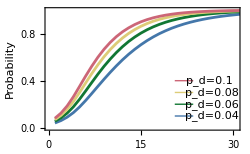

```mathematica
Show[ListLinePlot[{pend4,pend6,pend8,pend10},PlotRange->{{0,30.5},All},Frame->True,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Days after initial detection","Estimated probability outbreak has ended"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{20.5,0.4},{23.5,0.4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{20.5,0.3},{23.5,0.3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{20.5,0.2},{23.5,0.2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{20.5,0.1},{23.5,0.1}}]}],Graphics[Text["p_d=0.1",{26.2,0.4}]],Graphics[Text["p_d=0.08",{26.5,0.3}]],Graphics[Text["p_d=0.06",{26.5,0.2}]],Graphics[Text["p_d=0.04",{26.5,0.1}]]]
```

```mathematica
Population size conditional on not dying out at day 14
```

14 at conditional day dying not on out Population size

89

69

61

56

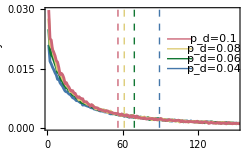

```mathematica
val=14;
s4=sizedist4[[val]];
s6=sizedist6[[val]];
s8=sizedist8[[val]];
s10=sizedist10[[val]];
y1=0.2;
y2=0.24;
y3=0.28;
y4=0.32;
cs4=s4;
For[i=2,i<=Length[s4],i++,
cs4[[i,2]]=cs4[[i,2]]+cs4[[i-1,2]];
];
cs6=s6;
For[i=2,i<=Length[s6],i++,
cs6[[i,2]]=cs6[[i,2]]+cs6[[i-1,2]];
];
cs8=s8;
For[i=2,i<=Length[s8],i++,
cs8[[i,2]]=cs8[[i,2]]+cs8[[i-1,2]];
];
cs10=s10;
For[i=2,i<=Length[s10],i++,
cs10[[i,2]]=cs10[[i,2]]+cs10[[i-1,2]];
];
Med[s_]:= Median[WeightedData[Map[First,s], Map[Last, s]]];
(*
med4=Sort[cs4,Abs[#1[[2]]-0.5]<Abs[#2[[2]]-0.5]&][[1,1]];
med6=Sort[cs6,Abs[#1[[2]]-0.5]<Abs[#2[[2]]-0.5]&][[1,1]];
med8=Sort[cs8,Abs[#1[[2]]-0.5]<Abs[#2[[2]]-0.5]&][[1,1]];
med10=Sort[cs10,Abs[#1[[2]]-0.5]<Abs[#2[[2]]-0.5]&][[1,1]];
*)
med4 = Med[s4]
med6 = Med[s6]
med8 = Med[s8]
med10 = Med[s10]
y1=0.015;
dy=0.0025;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1 = 95;
x2 = x1+20;
p1=Show[ListLinePlot[{s4[[2;;]],s6[[2;;]],s8[[2;;]],s10[[2;;]]},PlotRange->{{1,150},All},Frame->True,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Number of infected individuals","Day 14"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x2,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{x1,y3},{x2,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{x1,y2},{x2,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{x1,y1},{x2,y1}}]}],Graphics[Text["p_d=0.1",{132,y4}]],Graphics[Text["p_d=0.08",{132,y3}]],Graphics[Text["p_d=0.06",{132,y2}]],Graphics[Text["p_d=0.04",{132,y1}]],Graphics[{Dashed,fourParamChartStyle[[1]],Line[{{med4,0},{med4,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[2]],Line[{{med6,0},{med6,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[3]],Line[{{med8,0},{med8,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[4]],Line[{{med10,0},{med10,0.5}}]}]]
```

```mathematica
s = {{0,0.1}, {1,0.35}, {2, 0.25}, {3, 0.4}};
cs=s;
For[i=2,i<=Length[s],i++,
cs[[i,2]]=cs[[i,2]]+cs[[i-1,2]];
];

med=Sort[cs,Abs[#1[[2]]-0.5]<Abs[#2[[2]]-0.5]&][[1,1]]
med2= Median[WeightedData[Map[First,s], Map[Last, s]]]
```

1

2

```mathematica
Median outbreak sizes
```

Median outbreak sizes

```mathematica
{med4,med6,med8,med10}
```

{89,69,61,56}

```mathematica
Figure S1
```

Figure S1

```mathematica
Changes in mean population size conditional on not dying out over time
```

Changes conditional dying in mean not on out over population size time

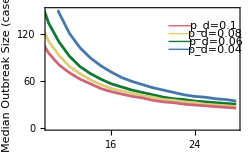

```mathematica
val=29;
y1=100;
dy=10;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1=21.5;
dx=2.25;
x2=26;
Show[ListLinePlot[{Table[FindMedianSize[sizedist4,i],{i,1,28}],Table[FindMedianSize[sizedist6,i],{i,1,28}],Table[FindMedianSize[sizedist8,i],{i,1,28}],Table[FindMedianSize[sizedist10,i],{i,1,28}]},Frame->True,PlotStyle->fourParamChartStyle,PlotRange->{{10,28},{0,150}},FrameLabel->{{"Median Outbreak Size (cases)",None},{"Days after detection","Estimates conditional on outbreak surviving"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x1+dx,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{x1,y3},{x1+dx,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{x1,y2},{x1+dx,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{x1,y1},{x1+dx,y1}}]}],Graphics[Text["p_d=0.1",{x2-0.15,y4}]],Graphics[Text["p_d=0.08",{x2,y3}]],Graphics[Text["p_d=0.06",{x2,y2}]],Graphics[Text["p_d=0.04",{x2,y1}]]]
```

```mathematica
Population size absolute at day 14
```

14 absolute at day Population size

0

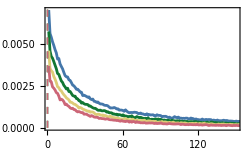

```mathematica
val=14;
s4=sizedist4[[val]];
s6=sizedist6[[val]];
s8=sizedist8[[val]];
s10=sizedist10[[val]];
s4[[;;,2]]=s4[[;;,2]]*(1-pend4[[val,2]]);
s6[[;;,2]]=s6[[;;,2]]*(1-pend6[[val,2]]);
s8[[;;,2]]=s8[[;;,2]]*(1-pend8[[val,2]]);
s10[[;;,2]]=s10[[;;,2]]*(1-pend10[[val,2]]);
s4[[1,2]]=pend4[[val,2]];
s6[[1,2]]=pend6[[val,2]];
s8[[1,2]]=pend8[[val,2]];
s10[[1,2]]=pend10[[val,2]];
(*Median outbreak sizes*)
cs4=s4;
For[i=2,i<=Length[s4],i++,
cs4[[i,2]]=cs4[[i,2]]+cs4[[i-1,2]];
];
cs6=s6;
For[i=2,i<=Length[s6],i++,
cs6[[i,2]]=cs6[[i,2]]+cs6[[i-1,2]];
];
cs8=s8;
For[i=2,i<=Length[s8],i++,
cs8[[i,2]]=cs8[[i,2]]+cs8[[i-1,2]];
];
cs10=s10;
For[i=2,i<=Length[s10],i++,
cs10[[i,2]]=cs10[[i,2]]+cs10[[i-1,2]];
];
cs4
Med[s_]:= Median[WeightedData[Map[First,s], Map[Last, s]]];
med4=Med[s4]
med6=Med[s6];
med8=Med[s8];
med10=Med[s10];
p1=Show[ListLinePlot[{s4[[2;;]],s6[[2;;]],s8[[2;;]],s10[[2;;]]},PlotRange->{{1,150},All},Frame->True,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Outbreak size (cases)","Day 14"}}, FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{13,y4},{15,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{13,y3},{15,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{13,y2},{15,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{13,y1},{15,y1}}]}],Graphics[Text["p_d=0.1",{17,y4}]],Graphics[Text["p_d=0.08",{17.2,y3}]],Graphics[Text["p_d=0.06",{17.2,y2}]],Graphics[Text["p_d=0.04",{17.2,y1}]],Graphics[{Dashed,fourParamChartStyle[[1]],Line[{{med4,0},{med4,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[2]],Line[{{med6,0},{med6,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[3]],Line[{{med8,0},{med8,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[4]],Line[{{med10,0},{med10,0.5}}]}]]
```

```mathematica
Time of spillover event
```

event of spillover Time

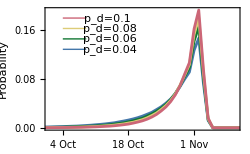

```mathematica
val=29;
y1=0.128;
dy=0.017;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1=-51;
dx=5;
x2=-41;
Show[ListLinePlot[{origdist4[[val]],origdist6[[val]],origdist8[[val]],origdist10[[val]]},PlotRange->{{-54,-14},All},Frame->True,Axes->False,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Date","Time of spillover event"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250,FrameTicks->{{Automatic,Automatic},{{{-23-28,"4 Oct"},{-23-21,"11 Oct"},{-23-14,"18 Oct"},{-23-7,"25 Oct"},{-23,"1 Nov"},{-23+7,"8 Nov"}},Automatic}}],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x1+dx,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{x1,y3},{x1+dx,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{x1,y2},{x1+dx,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{x1,y1},{x1+dx,y1}}]}],Graphics[Text["p_d=0.1",{x2-0.5,y4}]],Graphics[Text["p_d=0.08",{x2,y3}]],Graphics[Text["p_d=0.06",{x2,y2}]],Graphics[Text["p_d=0.04",{x2,y1}]]]
```

```mathematica
Maximum likelihood times relative to first observation
```

{first likelihood Maximum observation relative to,2 first likelihood Maximum observation relative to,3 first likelihood Maximum observation relative to,4 first likelihood Maximum observation relative to,5 first likelihood Maximum observation relative to,6 first likelihood Maximum observation relative to,7 first likelihood Maximum observation relative to,8 first likelihood Maximum observation relative to,9 first likelihood Maximum observation relative to,10 first likelihood Maximum observation relative to,11 first likelihood Maximum observation relative to,12 first likelihood Maximum observation relative to,13 first likelihood Maximum observation relative to,14 first likelihood Maximum observation relative to,15 first likelihood Maximum observation relative to,16 first likelihood Maximum observation relative to,17 first likelihood Maximum observation relative to,18 first likelihood Maximum observation relative to,19 first likelihood Maximum observation relative to,20 first likelihood Maximum observation relative to,21 first likelihood Maximum observation relative to,22 first likelihood Maximum observation relative to,23 first likelihood Maximum observation relative to,24 first likelihood Maximum observation relative to,25 first likelihood Maximum observation relative to,26 first likelihood Maximum observation relative to,27 first likelihood Maximum observation relative to,28 first likelihood Maximum observation relative to,29 first likelihood Maximum observation relative to,30 first likelihood Maximum observation relative to,31 first likelihood Maximum observation relative to,32 first likelihood Maximum observation relative to,90 first likelihood Maximum observation relative to}

```mathematica
Sort[origdist4[[val]],#1[[2]]>#2[[2]]&][[1,1]]
Sort[origdist6[[val]],#1[[2]]>#2[[2]]&][[1,1]]
Sort[origdist8[[val]],#1[[2]]>#2[[2]]&][[1,1]]
Sort[origdist10[[val]],#1[[2]]>#2[[2]]&][[1,1]]
```

-22

-22

-22

«1 more identical outputs»

```mathematica
Mean times relative to first observation
```

{first Mean observation relative to,2 first Mean observation relative to,3 first Mean observation relative to,4 first Mean observation relative to,5 first Mean observation relative to,6 first Mean observation relative to,7 first Mean observation relative to,8 first Mean observation relative to,9 first Mean observation relative to,10 first Mean observation relative to,11 first Mean observation relative to,12 first Mean observation relative to,13 first Mean observation relative to,14 first Mean observation relative to,15 first Mean observation relative to,16 first Mean observation relative to,17 first Mean observation relative to,18 first Mean observation relative to,19 first Mean observation relative to,20 first Mean observation relative to,21 first Mean observation relative to,22 first Mean observation relative to,23 first Mean observation relative to,24 first Mean observation relative to,25 first Mean observation relative to,26 first Mean observation relative to,27 first Mean observation relative to,28 first Mean observation relative to,29 first Mean observation relative to,30 first Mean observation relative to,31 first Mean observation relative to,32 first Mean observation relative to,90 first Mean observation relative to}

```mathematica
Total[Table[origdist4[[val,i,1]]*origdist4[[val,i,2]],{i,1,Length[origdist4[[val]]]}]]
Total[Table[origdist6[[val,i,1]]*origdist6[[val,i,2]],{i,1,Length[origdist6[[val]]]}]]
Total[Table[origdist8[[val,i,1]]*origdist8[[val,i,2]],{i,1,Length[origdist8[[val]]]}]]
Total[Table[origdist10[[val,i,1]]*origdist10[[val,i,2]],{i,1,Length[origdist10[[val]]]}]]
```

-27.5308

-26.4392

-25.7698

-25.3151

```mathematica
Final distribution of R0
```

distribution Final of R0

{0.00576671,0.0126546,0.0211411,0.0319306,0.0455402,0.062748,0.0831953,0.106341,0.121842,0.12153,0.101688,0.0759091,0.0543472,0.0393158,0.0280422,0.020475,0.0154575,0.0115216,0.00879648,0.00672036,0.00524834,0.00417994,0.00316694,0.00247183,0.00200622,0.00153401,0.00131505,0.00102751,0.000812511,0.00067929,0.000563218,0.000507819,0.000361409,0.000267759,0.000208404,0.000221594,0.000150367,0.000121349,0.000110797,0.0000830977}

{{0.1,0.00576671},{0.2,0.0184213},{0.3,0.0395624},{0.4,0.071493},{0.5,0.117033},{0.6,0.179781},{0.7,0.262976},{0.8,0.369318},{0.9,0.49116},{1.,0.61269},{1.1,0.714377},{1.2,0.790287},{1.3,0.844634},{1.4,0.883949},{1.5,0.911992},{1.6,0.932467},{1.7,0.947924},{1.8,0.959446},{1.9,0.968242},{2.,0.974963},{2.1,0.980211},{2.2,0.984391},{2.3,0.987558},{2.4,0.99003},{2.5,0.992036},{2.6,0.99357},{2.7,0.994885},{2.8,0.995912},{2.9,0.996725},{3.,0.997404},{3.1,0.997967},{3.2,0.998475},{3.3,0.998837},{3.4,0.999104},{3.5,0.999313},{3.6,0.999534},{3.7,0.999685},{3.8,0.999806},{3.9,0.999917},{4.,1.}}

{{0.1,0.00576671},{0.2,0.0126546},{0.3,0.0211411},{0.4,0.0319306},{0.5,0.0455402},{0.6,0.062748},{0.7,0.0831953},{0.8,0.106341},{0.9,0.121842},{1.,0.12153},{1.1,0.101688},{1.2,0.0759091},{1.3,0.0543472},{1.4,0.0393158},{1.5,0.0280422},{1.6,0.020475},{1.7,0.0154575},{1.8,0.0115216},{1.9,0.00879648},{2.,0.00672036},{2.1,0.00524834},{2.2,0.00417994},{2.3,0.00316694},{2.4,0.00247183},{2.5,0.00200622},{2.6,0.00153401},{2.7,0.00131505},{2.8,0.00102751},{2.9,0.000812511},{3.,0.00067929},{3.1,0.000563218},{3.2,0.000507819},{3.3,0.000361409},{3.4,0.000267759},{3.5,0.000208404},{3.6,0.000221594},{3.7,0.000150367},{3.8,0.000121349},{3.9,0.000110797},{4.,0.0000830977}}

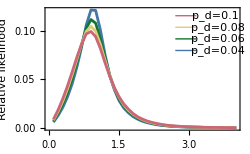

```mathematica
a4=accept4[[;;,-1,2]]/Total[accept4[[;;,-1,2]]]
ca4=a4;
For[i=2,i<=Length[ca4],i++,
ca4[[i]]=ca4[[i]]+ca4[[i-1]];
];
ca4=Partition[Riffle[Table[0.1*i,{i,1,40}],ca4],2]
a4=Partition[Riffle[Table[0.1*i,{i,1,40}],a4],2]

a6=accept6[[;;,-1,2]]/Total[accept6[[;;,-1,2]]];
ca6=a6;
For[i=2,i<=Length[ca6],i++,
ca6[[i]]=ca6[[i]]+ca6[[i-1]];
];
ca6=Partition[Riffle[Table[0.1*i,{i,1,40}],ca6],2];
a6=Partition[Riffle[Table[0.1*i,{i,1,40}],a6],2];

a8=accept8[[;;,-1,2]]/Total[accept8[[;;,-1,2]]];
ca8=a8;
For[i=2,i<=Length[ca8],i++,
ca8[[i]]=ca8[[i]]+ca8[[i-1]];
];
ca8=Partition[Riffle[Table[0.1*i,{i,1,40}],ca8],2];
a8=Partition[Riffle[Table[0.1*i,{i,1,40}],a8],2];

a10=accept10[[;;,-1,2]]/Total[accept10[[;;,-1,2]]];
ca10=a10;
For[i=2,i<=Length[ca10],i++,
ca10[[i]]=ca10[[i]]+ca10[[i-1]];
];
ca10=Partition[Riffle[Table[0.1*i,{i,1,40}],ca10],2];
a10=Partition[Riffle[Table[0.1*i,{i,1,40}],a10],2];

y1=0.08;
dy=0.012;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1=2.7;
dx=0.45;
x2=3.6;
Show[ListLinePlot[{a4,a6,a8,a10},Frame->True,Axes->False,PlotStyle->fourParamChartStyle,FrameLabel->{"R_0","Relative likelihood"},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x1+dx,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{x1,y3},{x1+dx,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{x1,y2},{x1+dx,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{x1,y1},{x1+dx,y1}}]}],Graphics[Text["p_d=0.1",{x2-0.05,y4}]],Graphics[Text["p_d=0.08",{x2,y3}]],Graphics[Text["p_d=0.06",{x2,y2}]],Graphics[Text["p_d=0.04",{x2,y1}]]]
```

```mathematica
Statistics of R0: Maximum likelihood
```

of Statistics (R0:likelihood Maximum)

```mathematica
Sort[a4,#1[[2]]>#2[[2]]&][[1,1]]
Sort[a6,#1[[2]]>#2[[2]]&][[1,1]]
Sort[a8,#1[[2]]>#2[[2]]&][[1,1]]
Sort[a10,#1[[2]]>#2[[2]]&][[1,1]]
```

0.9

0.9

0.9

«1 more identical outputs»

```mathematica
Statistics of R0: 95 per cent confidence interval
```

of Statistics (R0:95 cent confidence interval per)

```mathematica
ca4
```

{{0.1,0.00576671},{0.2,0.0184213},{0.3,0.0395624},{0.4,0.071493},{0.5,0.117033},{0.6,0.179781},{0.7,0.262976},{0.8,0.369318},{0.9,0.49116},{1.,0.61269},{1.1,0.714377},{1.2,0.790287},{1.3,0.844634},{1.4,0.883949},{1.5,0.911992},{1.6,0.932467},{1.7,0.947924},{1.8,0.959446},{1.9,0.968242},{2.,0.974963},{2.1,0.980211},{2.2,0.984391},{2.3,0.987558},{2.4,0.99003},{2.5,0.992036},{2.6,0.99357},{2.7,0.994885},{2.8,0.995912},{2.9,0.996725},{3.,0.997404},{3.1,0.997967},{3.2,0.998475},{3.3,0.998837},{3.4,0.999104},{3.5,0.999313},{3.6,0.999534},{3.7,0.999685},{3.8,0.999806},{3.9,0.999917},{4.,1.}}

```mathematica
{Select[ca4,#[[2]]<0.025&][[-1]],Select[ca4,#[[2]]>0.975&][[1]]}
{Select[ca6,#[[2]]<0.025&][[-1]],Select[ca6,#[[2]]>0.975&][[1]]}
{Select[ca8,#[[2]]<0.025&][[-1]],Select[ca8,#[[2]]>0.975&][[1]]}
{Select[ca10,#[[2]]<0.025&][[-1]],Select[ca10,#[[2]]>0.975&][[1]]}
```

{{0.2,0.0184213},{2.1,0.980211}}

{{0.2,0.0218272},{2.1,0.97704}}

{{0.2,0.0246347},{2.2,0.979584}}

{{0.1,0.00873164},{2.2,0.977666}}

```mathematica
Figure S2A
```

Figure S2A

```mathematica
Changes in the inferred posterior distribution for R0 with time given Subscript[p, d]=0.04
```

Set::write: Tag Times in Changes distribution for given in inferred posterior R0 the time «2» is Protected.

0.04

```mathematica
col2=Table[RGBColor[{Cos[2.31x-0.69],Sin[2.926x],Sin[2.772x-0.144]}],{x,0,1,1/27}]
```

{RGBColor[{0.7712460149971067, 0., -0.14350285172336283}],RGBColor[{0.8228179496180482, 0.10815837547764777, -0.04132156505470021}],RGBColor[{0.8683707329153034, 0.2150477668137401, 0.06129488683700954}],RGBColor[{0.9075711331016849, 0.31941407841089964, 0.16326583067337896}],RGBColor[{0.9401323879100587, 0.42003281707805756, 0.263517391143535}],RGBColor[{0.9658163023422827, 0.5157234585779733, 0.3609938000882835}],RGBColor[{0.9844349911345216, 0.6053632983024981, 0.4546685149944325}],RGBColor[{0.9958522531923037, 0.6879006235704856, 0.5435550297083055}],RGBColor[{0.9999845679409262, 0.7623670530024181, 0.6267172635187739}],RGBColor[{0.9968017063026193, 0.8278888981982057, 0.7032794192004101}],RGBColor[{0.9863269518309961, 0.8836974144155966, 0.7724352061998417}],RGBColor[{0.9686369303851207, 0.9291378199815968, 0.8334563318341858}],RGBColor[{0.9438610495891844, 0.9636769786153176, 0.8857001710791458}],RGBColor[{0.9121805521782997, 0.9869096545282654, 0.9286165341747794}],RGBColor[{0.8738271901554634, 0.9985632669131823, 0.961753460778003}],RGBColor[{0.8290815294586145, 0.9985010880386929, 0.9847619796425122}],RGBColor[{0.7782708975396367, 0.986723847427641, 0.9973997837010308}],RGBColor[{0.7217669888693595, 0.9633697232978549, 0.9995337818469013}],RGBColor[{0.6599831458849821, 0.9287127213657643, 0.9911415005417208}],RGBColor[{0.593371335270574, 0.8831594600337951, 0.9723113204884275}],RGBColor[{0.522418841690038, 0.827244399679806, 0.9432415458773894}],RGBColor[{0.44764470315883353, 0.7616235720216362, 0.90423831600744}],RGBColor[{0.36959591413074766, 0.6870668831279216, 0.8557123812749748}],RGBColor[{0.28884342407523306, 0.6044490803812398, 0.7981747774837799}],RGBColor[{0.20597796081687653, 0.5147394893750344, 0.7322314440302518}],RGBColor[{0.12160570919047721, 0.4189906411576828, 0.6585768426409192}],RGBColor[{0.03634387662362632, 0.3183259232562573, 0.5779866438645533}],RGBColor[{-0.049183821914170554, 0.2139263993661666, 0.4913095583387953}]}

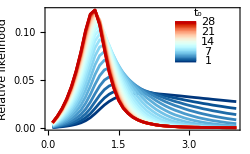

```mathematica
postt=Table[accept4[[;;,i,2]]/Total[accept4[[;;,i,2]]],{i,1,28}];
For[i=1,i<=Length[postt],i++,
postt[[i]]=Partition[Riffle[Table[i,{i,0.1,4.0,0.1}],postt[[i]]],2];
];

Show[ListLinePlot[postt,PlotRange->All,PlotStyle->Reverse[col2],Frame->True,FrameLabel->{"R_0","Relative likelihood"},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Table[Graphics[{Reverse[col2][[i]],Thickness[0.008],Line[{{2.7,0.07+0.0015*(i-1)},{3.15,0.07+0.0015*(i-1)}}]}],{i,1,28}],Graphics[Text["1",{3.4,0.07}]],Graphics[Text["7",{3.4,0.07+0.0015*6}]],Graphics[Text["14",{3.4,0.07+0.0015*13}]],Graphics[Text["21",{3.4,0.07+0.0015*20}]],Graphics[Text["28",{3.4,0.07+0.0015*27}]],Graphics[Text["t_o",{3.2,0.12}]]]
```

```mathematica
Figure S2B
```

Figure S2B

```mathematica
Changes in the inferred time of first infection with time given Subscript[p, d]=0.04
```

Set::write: Tag Times in Changes first given in infection inferred of the time time «2» is Protected.

0.04

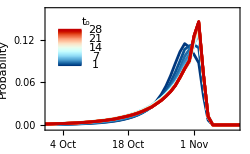

```mathematica
val=29;
y1=0.128;
dy=0.017;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1=-51;
dx=5;
x2=-41;
yy=0.085;
dyy=0.0018;
Show[Table[ListLinePlot[{origdist4[[val]]},PlotRange->{{-54,-14},{-0.004,0.162}},Frame->True,Axes->False,PlotStyle->Reverse[col2][[val]],FrameLabel->{{"Probability",None},{"Date","Time of spillover event"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250,FrameTicks->{{Automatic,Automatic},{{{-23-28,"4 Oct"},{-23-21,"11 Oct"},{-23-14,"18 Oct"},{-23-7,"25 Oct"},{-23,"1 Nov"},{-23+7,"8 Nov"}},Automatic}}],{val,1,28}],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x1+dx,y4}}]}],Table[Graphics[{Reverse[col2][[i]],Thickness[0.008],Line[{{-52,yy+dyy*(i-1)},{-47,yy+dyy*(i-1)}}]}],{i,1,28}],Graphics[Text["1",{-44,yy}]],Graphics[Text["7",{-44,yy+dyy*6}]],Graphics[Text["14",{-44,yy+dyy*13}]],Graphics[Text["21",{-44,yy+dyy*20}]],Graphics[Text["28",{-44,yy+dyy*27}]],Graphics[Text["t_o",{-46,0.145}]]]
```